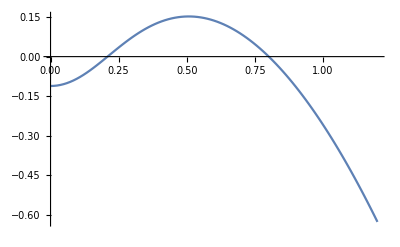

maxeig.csv

qvec.csv

```mathematica
(*Produces the theoretical prediction for the largest eigenvalue in Fig. 2d. This presumes that the largest eigenvalue is an outlier (as it is in Fig. 2). This could quite easily be extended to take into account the bulk region using the code in "eigenvalue_spectrum_theory"*)

Clear["Global`*"];
eff0 = 0.001;
(*Model parameters*)
(*Proportion of the population composed of prey and predator species respectively*)
gammafracu = 2.0/3.0;
gammafracv = 1.0/3.0;
(*Intraspecies interaction*)
du = 1.0;
dv = 1.0;
(*Interspecies interaction statistics*)
complexity =0.375;
f = 1.5;
ncmuuu =2.0 f;
ncmuuv = -2.0 f;
ncmuvu = 2.0 f;
ncmuvv = -1.0 f;
gammau = 0.5;
gammauv =-0.9;
gammav = -0.5;
(*Diffusion coefficients and wavenumbers*)
ddu = 1.0;
ddv = 5.0;
qmin= 0.0;
qmax = 1.2;
numq = 101;
qvec = Table[myq,{myq,qmin ,qmax,(qmax -qmin)/(numq -1)}];

maxeig =  Table[0,numq];

Monitor[
For[i = 1, i<numq +1, i++,
q = qvec[[i]];
s = NSolve[{-(u + du + q^2 ddu) mychix + gammafracu complexity gammau mychix^2 + gammafracv complexity gammauv mychiy mychix ==-1,  -(u + dv + q^2 ddv) mychiy  + gammafracu complexity gammauv mychix mychiy + gammafracv complexity gammav mychiy^2  ==-1,  u1 == (1 + complexity u1) (gammafracu mychix*Conjugate[mychix] +gammafracv mychiy*Conjugate[mychiy]), (gammafracu ncmuuu -1/mychix)(gammafracv ncmuvv -1/mychiy)-(gammafracv ncmuuv)( gammafracu ncmuvu) == 0},{mychix, mychiy, u, u1}];

eigx = {};
eigy = {};

For[k = 1, k<Length[s]+1, k++,
{chix, chiy, myu, myu1} = {mychix, mychiy, u, u1}/.s[[k]];
If[Re[myu1]>0,eigx = Append[eigx, Re[myu]];eigy = Append[eigy, Im[myu]];];
];

maxeig[[i]] = Max[Re[eigx]];

];,i];

plotpoints = Transpose[{qvec, maxeig}];
plot = ListLinePlot[plotpoints, PlotRange->All];
Show[plot,  PlotRange->All]

SetDirectory[NotebookDirectory[]];
Export["maxeig.csv",maxeig]
Export["qvec.csv",qvec]
```